```mathematica
ClearAll;
```

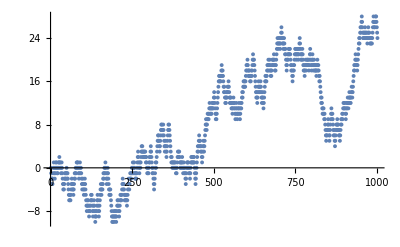

```mathematica
walk[n_]:=FoldList[Plus,0,Table[2Random[Integer]-1,{n}]];
ListPlot[walk[1000]]
```

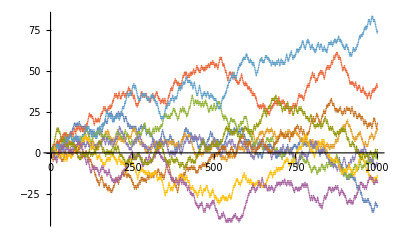

```mathematica
ListPlot[Table[walk[1000],{10}]]
```

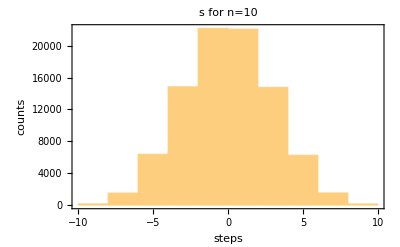

```mathematica
tData=Table[walk[1000]//N,{90000}];
Histogram[tData[[All,10]],{2},PlotLabel->"s for n=10",AxesLabel->{"steps","counts"},Frame->True,Axes->False]
```

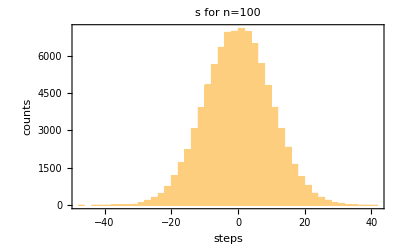

```mathematica
Histogram[tData[[All,100]],{2},PlotLabel->"s for n=100",AxesLabel->{"steps","counts"},Frame->True,Axes->False]
```

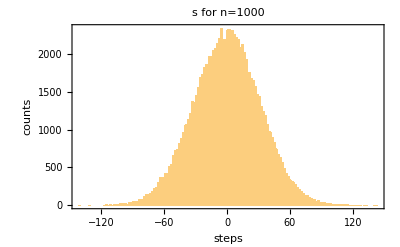

```mathematica
Histogram[tData[[All,1000]],{2},PlotLabel->" s for n=1000",AxesLabel->{"steps","counts"},Frame->True,Axes->False]
```

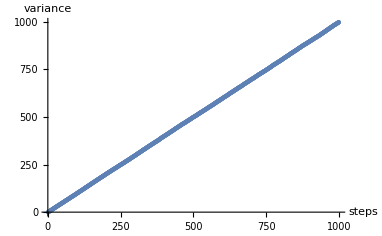

```mathematica
ListPlot[Table[{n,Variance[tData[[All,n]]]},{n,1,1000,1}],AxesLabel->{"steps","variance"}]
```

The relationship between variance and number of steps is proportional (linear).

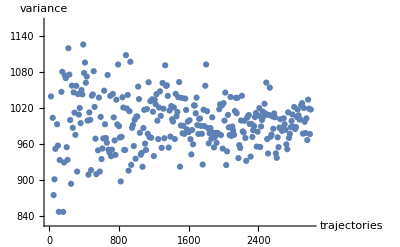

```mathematica
ListPlot[Table[{s,Variance[Table[walk[1000][[1000]]//N,{s}]]},{s,10,3000,10}],AxesLabel->{"trajectories","variance"}]
```